```mathematica
database = Import[FileNameJoin[{NotebookDirectory[],"sp500v3.wdx"}]];
```

```mathematica
First[database]//Keys
```

{Name,Symbol,Sector,FirstDate,LastDate,Dates,Prices,Returns,DatedPrices,DatedReturns}

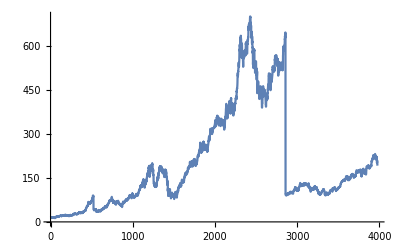
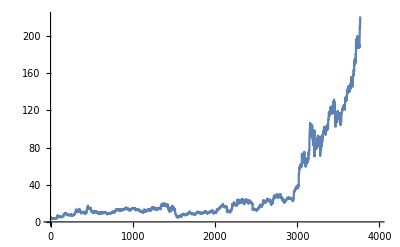
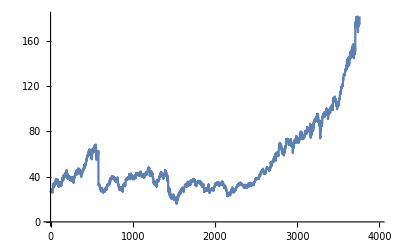
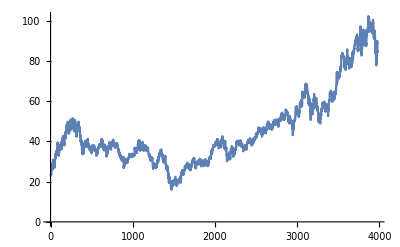
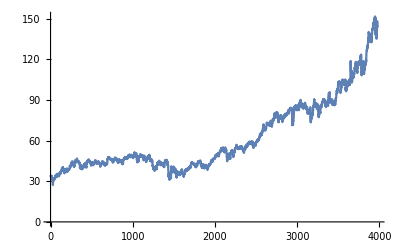
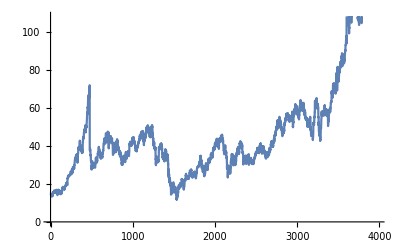
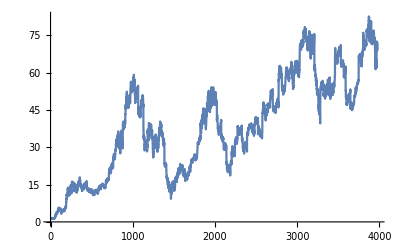
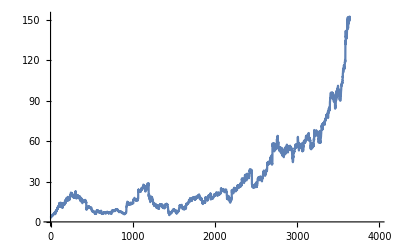

```mathematica
Map[ListLinePlot,Take[database[[All,"Prices"]],20]]
```